```mathematica
WE={D[u[x,t],{t,2}]-4( D[u[x,t],{x,2}])==0}
```

{u^(0,2)[x,t]-4 u^(2,0)[x,t]==0}

```mathematica
bc={u[0,t]==0,u[1,t]==0};
```

```mathematica
ic={u[x,0]==Sin[π x],u[x,1]==Sin[π x]}
```

{u[x,0]==Sin[π x],u[x,1]==Sin[π x]}

```mathematica
DSolve[Flatten[{WE,bc,ic}],u,{x,t}]
```

DSolve[{u^(0,2)[x,t]-4 u^(2,0)[x,t]==0,u[0,t]==0,u[1,t]==0,u[x,0]==Sin[π x],u[x,1]==Sin[π x]},u,{x,t}]

```mathematica
usol=First[u/.NDSolve[Flatten[{WE,bc,ic}],u,{x,0,1},{t,0,1}]]
```

InterpolatingFunction[…]

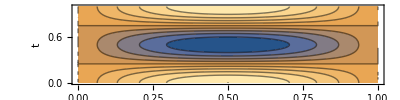

```mathematica
ContourPlot[usol[x,t],{x,0,1},{t,0,1},BaseStyle->FontSize->22,FrameLabel->{"x","t"},PlotLegends->Automatic,LabelStyle->FontSize->18,AspectRatio->1/4]
```

```mathematica
Length[Table[i,{i,0,1,1/10}]]
```

11

```mathematica
For[gridres=10,gridres<110,gridres+=10,
grid=Table[t,{t,0,1,1/gridres}];
tab=Table[usol[x,t],{x,grid},{t,grid}];
SetDirectory[NotebookDirectory[]];Export[StringJoin["wolfram_sln/","wave_sln_",ToString[gridres],".csv"],tab]
]
```